# Colored Jones Polynomials and the Volume Conjecture — Code to reproduce the paper

Author: Pratik Roy

Working with Mark Hughes, Vishnu Jejjala, P. Ramadevi, Vivek K. Singh

```mathematica
textstyle["This notebook can be used to reproduce most results and plots of our paper 'Colored Jones Polynomials and the Volume Conjecture'. The data for 3-dimensional colored Jones polynomials is also being made available at the DOI "]
```

This notebook can be used to reproduce most results and plots of our paper 'Colored Jones Polynomials and the Volume Conjecture'. The data for 3-dimensional colored Jones polynomials is also being made available at the DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
textstyle[text_]:=TextCell[Style[text,FontSize->15,FontFamily->"Gurmukhi MT"]]
```

```mathematica
textstyle["All the comments are generated like this one."]
```

All the comments are generated like this one.

These are the default Mathematica colors for the first three datasets in a plot.

```mathematica
col1=RGBColor[0.368417,0.506779,0.709798];
col2=RGBColor[0.880722,0.611041,0.142051];
col3=RGBColor[0.560181,0.691569,0.194885];
```

## Loading data

The data used here is made available at Zenodo, and can be found at https://doi.org/10.5281/zenodo.14900936.

Note that the Jones polynomials are stored as vectors of integers, where the first entry is the minimum power of q in the polynomial, the second entry is the maximum power of q, and the rest of the entries are coefficients of all powers of q from min to max.

```mathematica
namesall=Import["data-name-vol-J2-J3.h5",{"Data","names"}];
volsall=Import["data-name-vol-J2-J3.h5",{"Data","volumes"}];
jones2all=Import["data-name-vol-J2-J3.h5",{"Data","jones2"}];
jones3all=Import["data-name-vol-J2-J3.h5",{"Data","jones3"}];
```

These are the numbers of knots up to 13 crossings, and at 14 and 15 crossings.

```mathematica
len13=11921;
len14=18353;
len15=147022;
```

```mathematica
names13=namesall[[;;len13]];
vols13=volsall[[;;len13]];
jones213=jones2all[[;;len13]];
jones313=jones3all[[;;len13]];
```

```mathematica
names14=namesall[[len13+1;;len13+len14]];
vols14=volsall[[len13+1;;len13+len14]];
jones214=jones2all[[len13+1;;len13+len14]];
jones314=jones3all[[len13+1;;len13+len14]];
```

```mathematica
names15=namesall[[len13+len14+1;;]];
vols15=volsall[[len13+len14+1;;]];
jones215=jones2all[[len13+len14+1;;]];
jones315=jones3all[[len13+len14+1;;]];
```

```mathematica
vols1415=Join[vols14,vols15];
jones21415=Join[jones214,jones215];
jones31415=Join[jones314,jones315];
```

## Numerical analysis of (colored) Jones polynomial data

This section contains the analysis of polynomial data reported in Section 3 in the paper.

## Zeros of Jones polynomials

### Calculating and storing zeros

Convert the vector representation of polynomials to symbolic representation and use that to numerically solve for zeros of polynomials.

```mathematica
toPoly[vec_,q_]:=Module[{low,high,poly},
low=vec[[1]];
high=vec[[2]];
poly=Sum[vec[[i+3]] q^(low+i),{i,0,high-low}];
Return[poly];
];
```

```mathematica
zeros[vec_]:=ReIm[NSolve[toPoly[vec,q]][[;;,1,2]]]
```

```mathematica
zerodata[knot_]:={namesall[[knot]],zeros[jones2all[[knot]]],zeros[jones3all[[knot]]],volsall[[knot]]}
```

```mathematica
nameJ2zerosJ3zerosvol=ParallelMap[zerodata,Range[datasize]];
```

```mathematica
j2zeros=nameJ2zerosJ3zerosvol[[;;,2]];
```

```mathematica
j3zeros=nameJ2zerosJ3zerosvol[[;;,3]];
```

```mathematica
zeros3all=Flatten[ParallelMap[{zeros},jones3all],1];
```

```mathematica
zeros2all=Flatten[ParallelMap[zeros,jones2all],1];
```

```mathematica
zeros3UHP=DeleteCases[zeros3all,{a_,b_}/;b<0];
```

```mathematica
zeros2UHP=DeleteCases[zeros2all,{a_,b_}/;b<0];
```

```mathematica
Export["zeros-2-3-all-UHP.h5",{"jones3"->zeros3UHP,"jones2"->zeros2UHP}];
```

### Generating pixel data for zeros

Here we use the same strategy, as in the ML chapter, of pixelising a plot to generate an informative plot efficiently.

```mathematica
zeros2UHP=Import["zeros-2-3-all-UHP.h5",{"Data","jones2"}];
zeros3UHP=Import["zeros-2-3-all-UHP.h5",{"Data","jones3"}];
```

#### J_3

```mathematica
zeros3UHPsorted=Sort[zeros3UHP];
```

```mathematica
zeros3forplot=Cases[zeros3UHPsorted,{x_,y_}/;(x>-2.&&x<2.&&y<2.)];
```

```mathematica
ticksX=Range[-2.,2.,.005];
ticksY=Range[0.,2.,.005];
intervalsX=Table[{ticksX[[i]],ticksX[[i+1]]},{i,Length[ticksX]-1}];
intervalsY=Table[{ticksY[[i]],ticksY[[i+1]]},{i,Length[ticksY]-1}];
pixelsJ3=Tuples[{intervalsX,intervalsY}];
```

```mathematica
Length[intervalsX]
Length[intervalsY]
```

800

400

```mathematica
Length[pixelsJ3]
```

320000

```mathematica
xaxis=zeros3forplot[[;;,1]];
yaxis=zeros3forplot[[;;,2]];
```

```mathematica
xbins=BinLists[xaxis,.005];
xbinlengths=Length/@xbins;
xbinpos=Partition[FoldList[Plus,1,xbinlengths],2,1]/.{x_,y_}->{x,y-1};
xbinzeros=MapAt[Extract[zeros3forplot,#]&,MapApply[Range,xbinpos],{All,All}];
```

```mathematica
Length[xbinzeros]==Length[intervalsX]
```

True

```mathematica
pixelCountsJ3=Table[0,Length[pixelsJ3]];
SetSharedVariable[pixelCountsJ3];
```

```mathematica
ParallelMap[
Table[
If[
intervalsY[[j,1]]<=xbinzeros[[#,i,2]]<intervalsY[[j,2]],
pixelCountsJ3[[Length[intervalsY](#-1)+j]]+=1
]
,{i,Length[xbinzeros[[#]]]},{j,Length[intervalsY]}
]&
,Range[Length[xbinzeros]]
];
```

#### J_2

```mathematica
zeros2UHPsorted=Sort[zeros2UHP];
```

```mathematica
zeros2forplot=Cases[zeros2UHPsorted,{x_,y_}/;(x>-2.&&x<2.&&y<2.)];
```

```mathematica
ticksX=Range[-2.,2.,.005];
ticksY=Range[0.,2.,.005];
intervalsX=Table[{ticksX[[i]],ticksX[[i+1]]},{i,Length[ticksX]-1}];
intervalsY=Table[{ticksY[[i]],ticksY[[i+1]]},{i,Length[ticksY]-1}];
pixelsJ2=Tuples[{intervalsX,intervalsY}];
```

```mathematica
intervalsX[[1]]
```

{-2.,-1.995}

```mathematica
intervalsY[[1]]
```

{0.,0.005}

```mathematica
Length[pixelsJ2]
```

320000

```mathematica
xaxis=zeros2forplot[[;;,1]];
yaxis=zeros2forplot[[;;,2]];
```

```mathematica
xbins=BinLists[xaxis,.005];
xbinlengths=Length/@xbins;
xbinpos=Partition[FoldList[Plus,1,xbinlengths],2,1]/.{x_,y_}->{x,y-1};
xbinzeros=MapAt[Extract[zeros2forplot,#]&,MapApply[Range,xbinpos],{All,All}];
```

```mathematica
Length[xbinzeros]==Length[intervalsX]
```

True

```mathematica
pixelCountsJ2=Table[0,Length[pixelsJ2]];
SetSharedVariable[pixelCountsJ2];
```

```mathematica
ParallelMap[
Table[
If[
intervalsY[[j,1]]<=xbinzeros[[#,i,2]]<intervalsY[[j,2]],
pixelCountsJ2[[Length[intervalsY](#-1)+j]]+=1
]
,{i,Length[xbinzeros[[#]]]},{j,Length[intervalsY]}
]&
,Range[Length[xbinzeros]]
];
```

### Plotting zeros

#### J_3

```mathematica
pxcountsJ3=Union[pixelCountsJ3];
```

```mathematica
maxJ3=Max[pixelCountsJ3]
```

459770

```mathematica
maxJ3alt=pxcountsJ3[[-2]]
```

64326

```mathematica
lenX=800;
lenY=400;
```

```mathematica
satfn[satmin_,num_,max_]:=If[num==0,0,satmin*(1./satmin)^(Log[num]/Log[max])]
```

```mathematica
minsat=.2;
```

```mathematica
pxJ3tally=pixelCountsJ3//Tally//Sort
```

{{0,175104},{1,33815},{2,18580},{3,11896},{4,8554},{5,6259},{6,4914},{7,3942},{8,3220},{9,2731},{10,2349},{11,2035},{12,1752},{13,1645},{14,1558},{15,1397},{16,1378},{17,1239},{18,1217},{19,1106},{20,1118},{21,1053},{22,988},{23,995},{24,899},{25,857},{26,832},{27,812},{28,752},{29,779},{30,706},{31,705},{32,673},{33,664},{34,629},{35,615},{36,572},{37,533},{38,542},{39,521},{40,479},{41,517},{42,475},{43,458},{44,442},{45,452},{46,407},{47,432},{48,381},{49,368},{50,351},{51,389},{52,298},{53,313},{54,292},{55,237},{56,267},{57,226},{58,236},{59,217},{60,236},{61,198},{62,206},{63,172},{64,182},{65,170},{66,160},{67,144},{68,160},{69,126},{70,156},{71,148},{72,155},{73,130},{74,149},{75,148},{76,154},{77,131},{78,137},{79,123},{80,128},{81,136},{82,126},{83,143},{84,121},{85,130},{86,101},{87,129},{88,144},{89,115},{90,115},{91,130},{92,105},{93,106},{94,116},{95,102},{96,124},{97,102},{98,93},{99,95},{100,108},{101,114},{102,110},{103,95},{104,100},{105,98},{106,95},{107,99},{108,81},{109,97},{110,92},{111,84},{112,91},{113,98},{114,98},{115,78},{116,89},{117,78},{118,69},{119,91},{120,61},{121,73},{122,82},{123,73},{124,71},{125,90},{126,87},{127,77},{128,72},{129,62},{130,68},{131,72},{132,73},{133,81},{134,60},{135,55},{136,65},{137,75},{138,56},{139,59},{140,68},{141,49},{142,66},{143,66},{144,73},{145,49},{146,58},{147,63},{148,61},{149,86},{150,57},{151,48},{152,54},{153,58},{154,59},{155,52},{156,54},{157,53},{158,55},{159,49},{160,46},{161,46},{162,43},{163,52},{164,49},{165,36},{166,52},{167,42},{168,27},{169,42},{170,42},{171,47},{172,46},{173,41},{174,41},{175,45},{176,27},{177,30},{178,44},{179,30},{180,35},{181,19},{182,44},{183,35},{184,38},{185,32},{186,21},{187,27},{188,24},{189,16},{190,25},{191,24},{192,21},{193,23},{194,23},{195,26},{196,24},{197,18},{198,17},{199,24},{200,15},{201,16},{202,20},{203,13},{204,23},{205,16},{206,10},{207,15},{208,11},{209,20},{210,12},{211,11},{212,12},{213,15},{214,15},{215,18},{216,14},{217,13},{218,10},{219,12},{220,7},{221,15},{222,12},{223,9},{224,12},{225,11},{226,10},{227,6},{228,10},{229,9},{230,6},{231,7},{232,6},{233,9},{234,11},{235,8},{236,5},{237,10},{238,9},{239,8},{240,4},{241,7},{242,5},{243,8},{244,7},{245,5},{246,4},{247,8},{248,7},{249,7},{250,7},{251,7},{252,7},{253,2},{254,9},{255,5},{256,10},{258,6},{259,8},{260,1},{261,6},{262,2},{263,4},{264,5},{265,9},{266,1},{267,4},{268,4},{269,4},{270,7},{271,11},{272,6},{273,3},{274,7},{275,6},{276,2},{277,3},{278,7},{279,6},{280,6},{281,3},{282,3},{283,4},{284,4},{285,2},{286,2},{288,4},{289,5},{290,4},{291,4},{292,5},{293,8},{294,5},{295,2},{296,3},{297,3},{298,2},{299,3},{300,5},{301,4},{302,1},{303,3},{304,4},{305,2},{306,4},{307,3},{308,2},{309,1},{310,4},{311,3},{312,1},{313,4},{314,4},{315,3},{317,3},{318,3},{319,2},{320,5},{321,2},{322,1},{323,2},{324,5},{326,1},{327,5},{328,2},{329,1},{332,1},{333,1},{335,1},{336,2},{337,3},{338,4},{339,1},{340,2},{341,4},{342,2},{343,3},{344,2},{345,1},{346,2},{347,1},{348,2},{349,4},{350,2},{351,1},{352,1},{353,4},{354,2},{356,1},{357,3},{358,2},{359,2},{360,1},{361,2},{362,1},{363,2},{365,2},{366,2},{367,2},{369,1},{371,2},{373,4},{376,2},{377,1},{380,2},{383,1},{384,2},{386,1},{388,3},{389,2},{392,3},{394,1},{395,2},{397,2},{398,2},{399,1},{400,4},{402,3},{403,1},{404,3},{405,2},{406,1},{409,1},{412,1},{413,1},{414,1},{415,1},{417,2},{419,3},{420,2},{421,1},{422,1},{426,1},{427,3},{428,1},{432,1},{433,1},{434,2},{435,3},{437,1},{438,1},{440,1},{442,1},{444,1},{445,1},{446,1},{448,2},{449,1},{451,1},{452,1},{453,2},{454,1},{455,2},{456,1},{457,2},{458,2},{459,2},{463,1},{464,1},{466,1},{467,2},{468,2},{469,4},{474,1},{475,1},{477,1},{478,1},{479,1},{484,1},{485,1},{487,2},{488,1},{489,2},{490,1},{492,2},{495,1},{496,1},{497,3},{502,1},{509,1},{510,2},{511,2},{512,1},{514,1},{516,3},{517,3},{518,1},{520,1},{521,1},{522,2},{526,1},{527,2},{529,1},{530,2},{533,2},{536,1},{537,1},{539,1},{540,1},{541,2},{542,1},{546,1},{548,1},{551,2},{556,1},{558,1},{563,1},{564,1},{567,1},{569,2},{570,1},{571,1},{572,2},{574,1},{575,2},{578,2},{583,1},{584,1},{585,2},{587,1},{592,1},{593,1},{597,1},{599,3},{601,1},{602,1},{604,2},{606,2},{607,1},{608,1},{610,1},{611,2},{612,1},{613,2},{614,1},{615,2},{616,1},{617,3},{618,1},{620,1},{621,1},{624,1},{627,2},{628,1},{630,1},{632,3},{633,1},{635,2},{641,1},{643,1},{645,1},{649,1},{650,2},{652,2},{654,2},{655,1},{656,1},{657,1},{658,1},{660,2},{661,2},{663,2},{664,3},{665,1},{668,2},{670,1},{671,2},{672,1},{673,2},{674,2},{676,1},{677,2},{678,3},{681,1},{685,2},{686,1},{687,1},{689,2},{690,1},{694,1},{698,1},{699,1},{701,1},{702,2},{704,2},{706,1},{707,1},{708,1},{709,2},{712,1},{713,2},{717,1},{719,2},{721,1},{722,1},{723,1},{724,1},{729,3},{735,1},{739,1},{740,1},{749,2},{750,1},{751,1},{754,1},{756,1},{762,1},{766,1},{767,1},{770,1},{777,1},{780,1},{781,1},{783,2},{788,1},{791,2},{797,1},{798,1},{799,1},{805,1},{809,1},{811,2},{812,1},{818,1},{823,1},{824,1},{826,1},{828,1},{829,2},{833,2},{835,2},{836,1},{847,1},{851,1},{853,1},{857,1},{867,1},{868,1},{870,1},{871,1},{873,1},{874,1},{877,1},{879,2},{884,1},{889,1},{891,1},{895,1},{902,1},{905,1},{906,1},{910,1},{911,3},{912,1},{914,1},{915,1},{917,1},{921,1},{926,1},{927,1},{928,1},{929,1},{956,1},{960,1},{966,1},{968,1},{978,1},{980,1},{981,1},{985,1},{986,1},{991,2},{992,1},{993,1},{994,1},{999,1},{1004,2},{1005,1},{1012,1},{1020,1},{1024,2},{1026,1},{1034,1},{1035,1},{1048,1},{1059,1},{1060,1},{1072,1},{1079,1},{1085,1},{1099,1},{1102,1},{1104,1},{1105,1},{1111,1},{1112,1},{1113,1},{1125,2},{1128,1},{1132,1},{1134,1},{1135,1},{1155,1},{1165,1},{1168,1},{1171,2},{1174,1},{1181,1},{1184,1},{1191,1},{1193,1},{1212,2},{1226,1},{1233,1},{1237,1},{1253,1},{1262,1},{1269,1},{1270,1},{1291,1},{1306,1},{1309,1},{1311,2},{1316,1},{1324,1},{1331,1},{1332,1},{1338,1},{1339,1},{1346,2},{1347,1},{1350,1},{1374,1},{1389,1},{1409,1},{1420,1},{1432,1},{1461,1},{1483,1},{1489,1},{1491,1},{1493,1},{1519,1},{1526,1},{1530,1},{1538,1},{1560,1},{1573,1},{1581,1},{1589,1},{1597,1},{1635,1},{1649,1},{1657,1},{1677,1},{1681,1},{1689,1},{1692,1},{1723,1},{1755,1},{1770,1},{1801,1},{1804,1},{1808,1},{1827,1},{1829,1},{1833,1},{1851,1},{1868,1},{1889,1},{1906,2},{1933,1},{1963,1},{1978,1},{1991,1},{2005,1},{2022,1},{2064,1},{2130,1},{2142,1},{2165,1},{2228,1},{2246,1},{2271,1},{2279,1},{2325,1},{2434,1},{2471,1},{2571,1},{2576,1},{2595,1},{2657,1},{2778,1},{2781,1},{2823,1},{2836,1},{2857,1},{2972,1},{2992,1},{3000,1},{3011,1},{3030,1},{3079,1},{3140,1},{3153,1},{3246,1},{3249,1},{3306,1},{3401,1},{3432,1},{3449,1},{3456,1},{3472,1},{3591,1},{3601,1},{3637,1},{3642,1},{3649,1},{3657,1},{3658,1},{3664,1},{3670,1},{3699,1},{3720,1},{3835,1},{3857,1},{3867,1},{3896,1},{3974,1},{4151,1},{4344,1},{4552,1},{4709,1},{4743,1},{4907,1},{4937,1},{4953,1},{5067,1},{5094,1},{5116,1},{5323,1},{11729,1},{23875,1},{23969,1},{43148,1},{43309,1},{44596,1},{45431,1},{64326,1},{459770,1}}

```mathematica
zerosJ3=ArrayPlot[Apply[Hue,Transpose[Reverse/@Table[{1.,satfn[minsat,pixelCountsJ3[[lenY(i-1)+j]],maxJ3alt],1},{i,lenX},{j,lenY}]],{2}],Frame->False,Axes->True,DataRange->{{-2.,2.},{0.,2.}},AspectRatio->1/2,PlotLegends->BarLegend[{Hue[1,satfn[minsat,#,maxJ3alt],1]&,{1,maxJ3alt}},{1,10,100,1000,10000,maxJ3alt}],ImageSize->1000]
```

-Graphics-

#### J_2

```mathematica
pxcountsJ2=Union[pixelCountsJ2];
```

```mathematica
maxJ2=Max[pixelCountsJ2]
```

62870

```mathematica
maxJ2alt=pxcountsJ2[[-2]]
```

7959

```mathematica
lenX=800;
lenY=400;
```

```mathematica
satfn[satmin_,num_,max_]:=If[num==0,0,satmin*(1./satmin)^(Log[num]/Log[max])]
```

```mathematica
minsat=.2;
```

```mathematica
zerosJ2=ArrayPlot[Apply[Hue,Transpose[Reverse/@Table[{1.,satfn[minsat,pixelCountsJ2[[lenY(i-1)+j]],maxJ2alt],1},{i,lenX},{j,lenY}]],{2}],Frame->False,Axes->True,DataRange->{{-2.,2.},{0.,2.}},AspectRatio->1/2,PlotLegends->BarLegend[{Hue[1,satfn[minsat,#,maxJ2alt],1]&,{1,maxJ2alt}},{1,10,100,1000,maxJ2alt}],ImageSize->1000]
```

-Graphics-

#### J_3 around 1

```mathematica
satfn[satmin_,num_,max_]:=If[num==0,0,satmin*(1./satmin)^(Log[num]/Log[max])]
```

```mathematica
maxAround1=Max[pixelCountsAround1]
```

29

```mathematica
lenX=400;
lenY=400;
```

```mathematica
minsat=.2;
```

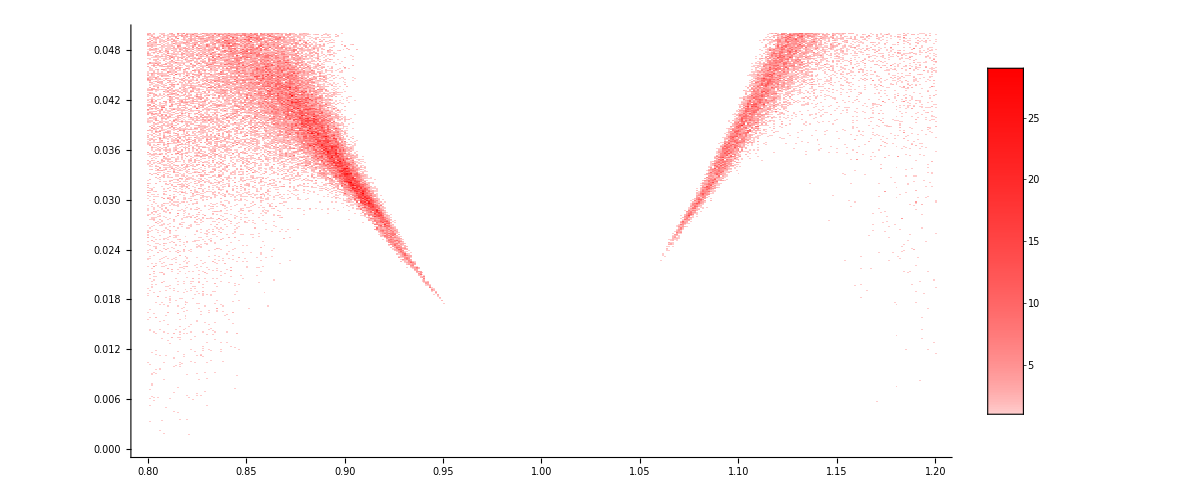

```mathematica
zerosJ3Around1=ArrayPlot[Apply[Hue,Transpose[Reverse/@Table[{1.,satfn[minsat,pixelCountsAround1[[lenY(i-1)+j]],maxAround1],1,.8},{i,lenX},{j,lenY}]],{2}],Frame->False,Axes->True,DataRange->{{.8,1.2},{0.,0.05}},AspectRatio->1/2,PlotLegends->BarLegend[{Hue[1,satfn[minsat,#,maxAround1],1]&,{1,maxAround1}}],ImageSize->1000]
```

## Degrees of polynomials

```mathematica
satfn[huemin_,num_,max_]:=If[num==0,0,huemin*(1./huemin)^(Log[num]/Log[max])]
huefn[satmin_,num_,max_]:=Hue[1.,satfn[satmin,num,max],1.]
```

```mathematica
Table[huefn[.2,i,10],{i,10}]
```

{Hue[1., 0.2, 1.],Hue[1., 0.32466908199276523, 1.],Hue[1., 0.4310458231742096, 1.],Hue[1., 0.5270500640101246, 1.],Hue[1., 0.616011844344503, 1.],Hue[1., 0.6997362585339321, 1.],Hue[1., 0.7793421698597509, 1.],Hue[1., 0.8555843022319762, 1.],Hue[1., 0.9290025083796595, 1.],Hue[1., 1., 1.]}

```mathematica
minsat=.3;
```

```mathematica
talliedmin=Sort[Tally[Transpose[{jones2all[[;;,1]],jones3all[[;;,1]]}]]];
```

```mathematica
maxmincoeff=Max[talliedmin[[;;,2]]]
```

2560

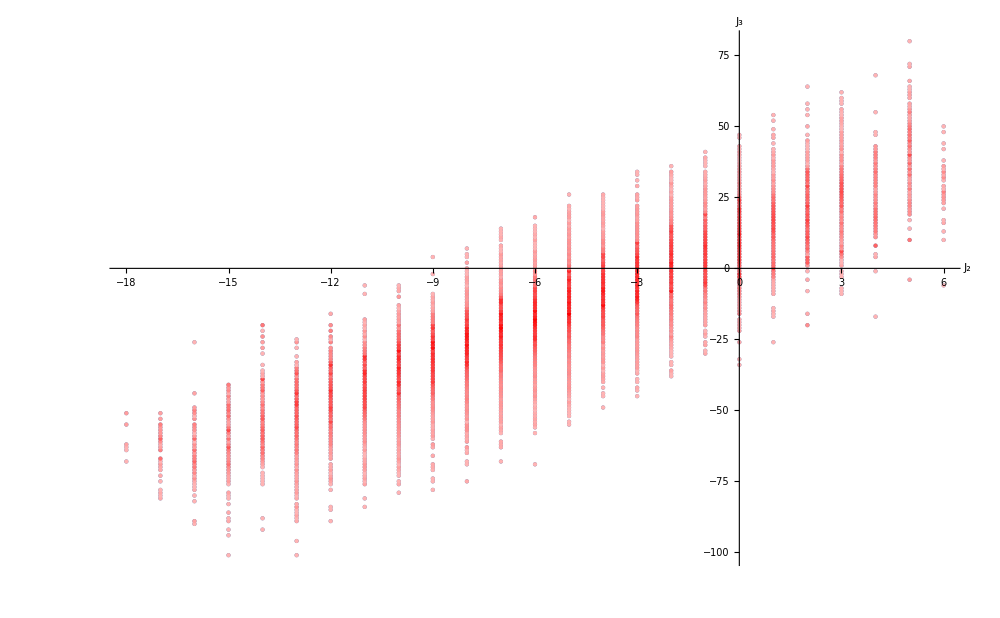

```mathematica
j2j3mindegs=ListPlot[MapApply[Style,Transpose[{talliedmin[[;;,1]],huefn[minsat,#,maxmincoeff]&/@talliedmin[[;;,2]]}]],AxesOrigin->{0,0}(*,PlotLegends->BarLegend[{huefn[minsat,#,maxmincoeff]&,{1,maxmincoeff}}]*),ImageSize->1000,AxesLabel->{"J_2","J_3"},LabelStyle->Directive[FontSize->15,Black],PlotStyle->PointSize[.003]]
```

```mathematica
talliedmax=Sort[Tally[Transpose[{jones2all[[;;,2]],jones3all[[;;,2]]}]]];
```

```mathematica
maxmaxcoeff=Max[talliedmax[[;;,2]]]
```

2368

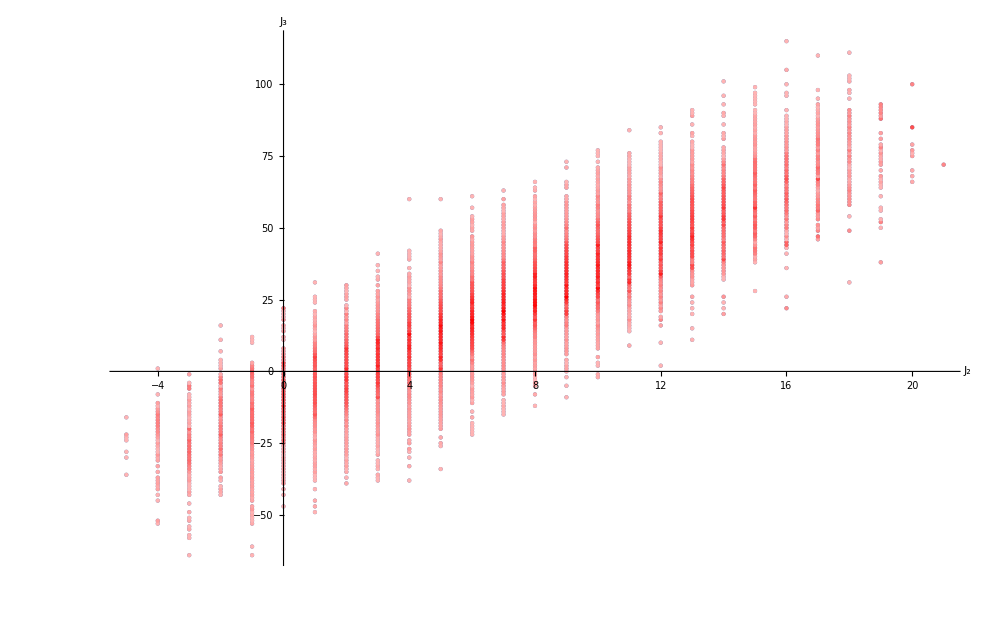

```mathematica
j2j3maxdegs=ListPlot[MapApply[Style,Transpose[{talliedmax[[;;,1]],huefn[minsat,#,maxmaxcoeff]&/@talliedmax[[;;,2]]}]],AxesOrigin->{0,0}(*,PlotLegends->BarLegend[{huefn[minsat,#,maxmaxcoeff]&,{1,maxmaxcoeff}}]*),ImageSize->1000,AxesLabel->{"J_2","J_3"},LabelStyle->Directive[FontSize->15,Black],PlotStyle->PointSize[.003]]
```

```mathematica
talliedj2=Sort[Tally[Transpose[{jones2NKall[[;;,1]],jones2NKall[[;;,2]]}]]];
```

```mathematica
maxj2=Max[talliedj2[[;;,2]]]
```

9063

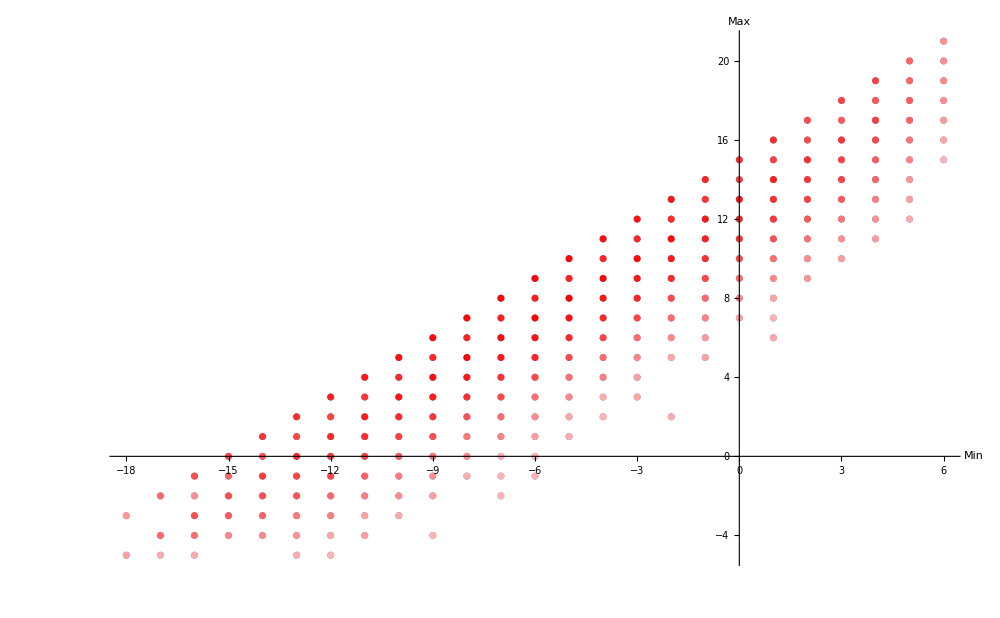

```mathematica
j2minmaxdegs=ListPlot[MapApply[Style,Transpose[{talliedj2[[;;,1]],huefn[minsat,#,maxj2]&/@talliedj2[[;;,2]]}]],AxesOrigin->{0,0},ImageSize->1000,AxesLabel->{"Min","Max"},LabelStyle->Directive[FontSize->15,Black],PlotStyle->PointSize[.005]]
```

```mathematica
talliedj3=Sort[Tally[Transpose[{jones3all[[;;,1]],jones3all[[;;,2]]}]]];
```

```mathematica
maxj3=Max[talliedj3[[;;,2]]]
```

1950

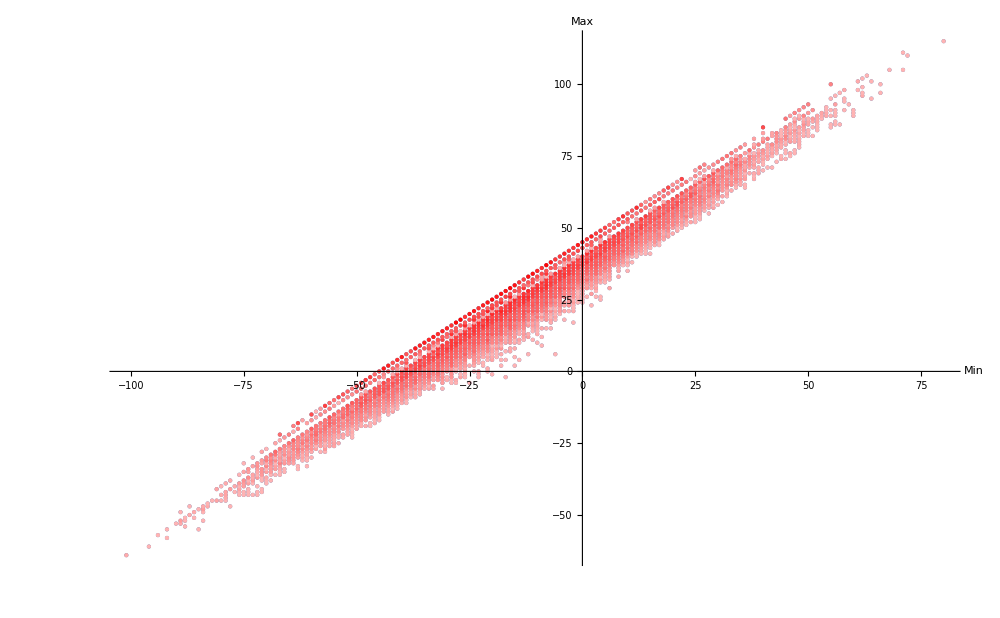

```mathematica
j3minmaxdegs=ListPlot[MapApply[Style,Transpose[{talliedj3[[;;,1]],huefn[minsat,#,maxj3]&/@talliedj3[[;;,2]]}]],AxesOrigin->{0,0},ImageSize->1000,AxesLabel->{"Min","Max"},LabelStyle->Directive[FontSize->15,Black],PlotStyle->PointSize[.003]]
```

```mathematica
jones2min=jones2NKall[[;;,1]];
jones2max=jones2NKall[[;;,2]];
jones3min=jones3all[[;;,1]];
jones3max=jones3all[[;;,2]];
```

```mathematica
modedeg[degslist_]:=Extract[Tally[degslist],Position[Tally[degslist][[;;,2]],Tally[degslist][[;;,2]]//Max]][[1]]
```

```mathematica
j2minmode=modedeg[jones2min]
j2maxmode=modedeg[jones2max]
j3minmode=modedeg[jones3min]
j3maxmode=modedeg[jones3max]
```

{-6,156240}

{8,155587}

{-16,5346}

{18,5290}

```mathematica
1.j3minmode[[1]]/j2minmode[[1]]
1.j3maxmode[[1]]/j2maxmode[[1]]
```

2.66667

2.25

```mathematica
j2minmean=jones2min//Mean//N
j2maxmean=jones2max//Mean//N
j3minmean=jones3min//Mean//N
j3maxmean=jones3max//Mean//N
```

-5.85956

8.0436

-15.0273

24.7267

```mathematica
j3minmean/j2minmean
j3maxmean/j2maxmean
```

2.56458

3.07409

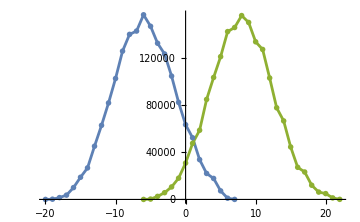

```mathematica
j2minmaxdist=ListPlot[{Sort[Tally[jones2min]],Sort[Tally[jones2max]]},Joined->True,PlotStyle->{col1,col3},ImageSize->Medium,Mesh->All,LabelStyle->Directive[FontSize->10,Black]]
```

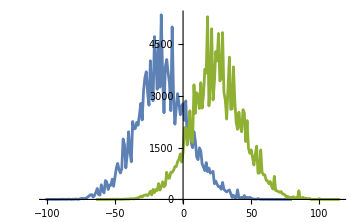

```mathematica
j3minmaxdist=ListPlot[{Sort[Tally[jones3min]],Sort[Tally[jones3max]]},Joined->True,PlotStyle->{col1,col3},ImageSize->Medium,LabelStyle->Directive[FontSize->10,Black]]
(*ListPlot[Sort[Tally[jones3max]],Joined->True]*)
```

```mathematica
j3maxvar=Variance[jones3max]//N
```

375.835

```mathematica
guessJ3max[x_]:=4000SetPrecision[Exp[-SetPrecision[(x-j3maxmean)^2/SetPrecision[2j3maxvar,100],100]],100]
```

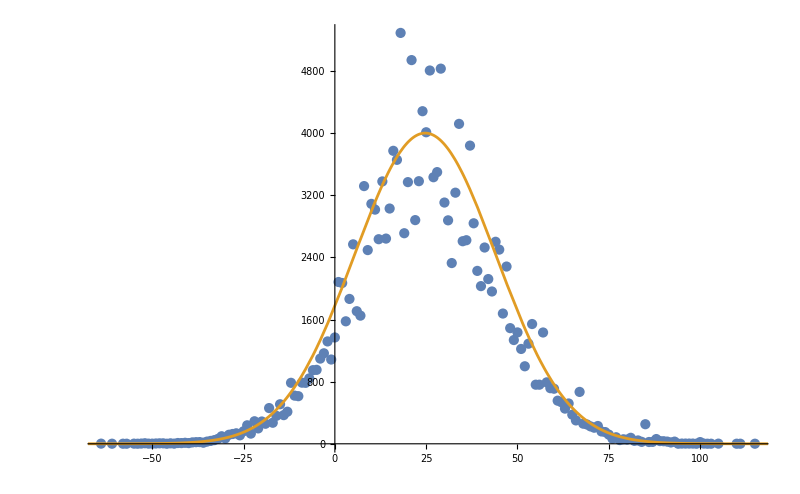

```mathematica
j3maxfit=Show[Tally[jones3max]//ListPlot,Plot[guessJ3max[x],{x,j3maxmean-100,j3maxmean+100},PlotRange->All,PlotStyle->col2],ImageSize->800,LabelStyle->Directive[FontSize->15,Black]]
```

## Quadratic relation between |J_2(ⅇ^(ⅈ ℼ))| and |J_3(ⅇ^(2ⅈ π/3))|

```mathematica
toPoly[vec_,q_]:=Sum[vec[[i+3]] q^(vec[[1]]+i),{i,0,vec[[2]]-vec[[1]]}]
```

```mathematica
jones2ⅈπ=toPoly[#,-1]&/@jones2all;
```

```mathematica
jones3ⅈπ2by3=toPoly[#,E^(2π ⅈ/3)]&/@jones3all;
```

```mathematica
absjones3ⅈπ2by3=Abs[jones3ⅈπ2by3];
```

```mathematica
jones2at1=toPoly[#,1]&/@jones2all;
jones3at1=toPoly[#,1]&/@jones3all;
```

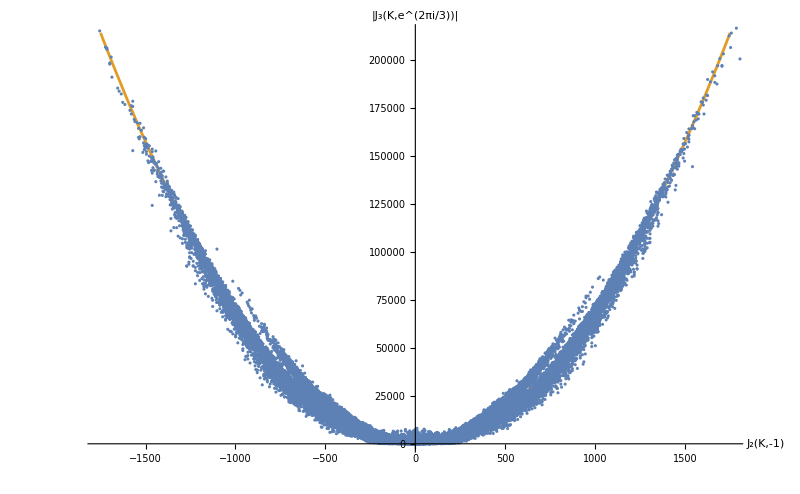

```mathematica
Show[Plot[x^2/10^1.155,{x,-1750,1750},PlotStyle->col2,AxesLabel->{"J_2(K,-1)","|J_3(K,e^(2πi/3))|"},LabelStyle->Directive[FontSize->15,Black],ImageSize->800],ListPlot[RandomSample[Transpose[{jones2ⅈπ,absjones3ⅈπ2by3}],40000],PlotRange->{{-1750,1750},All},ImageSize->800]]
```

```mathematica
DensityPlot
```

```mathematica
jones2ⅈπ//Min
```

-1947

```mathematica
1750^2/10^1.155
```

214327.

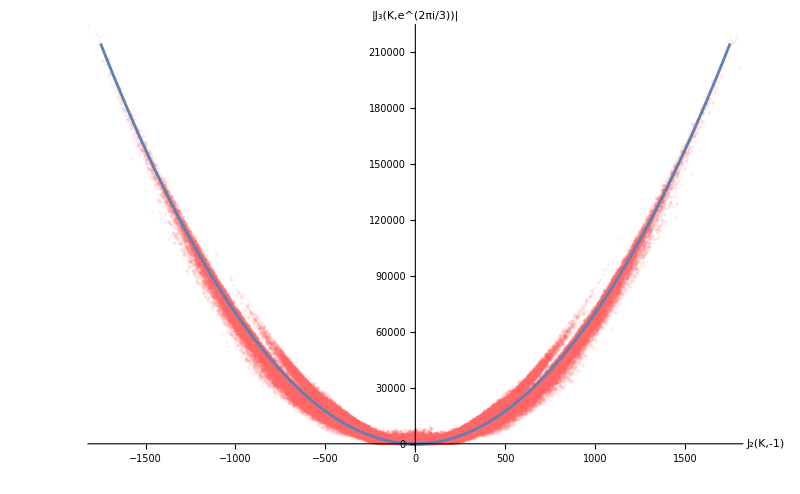

```mathematica
Show[ListPlot[Transpose[{jones2ⅈπ,absjones3ⅈπ2by3}],PlotStyle->Hue[1.,.6,1.,.1],AxesLabel->{"J_2(K,-1)","|J_3(K,e^(2πi/3))|"},LabelStyle->Directive[FontSize->15,Black],ImageSize->800],Plot[x^2/10^1.155,{x,-1750,1750},PlotStyle->Directive[col1],AxesLabel->{"J_2(K,-1)","|J_3(K,e^(2πi/3))|"},LabelStyle->Directive[FontSize->18,Black]],PlotRange->{{-1750,1750},{0,220000}}]
```

```mathematica
jones2at1//Flatten//Union
jones3at1//Flatten//Union
```

{1}

{1}

### Plotting this using pixel data

```mathematica
<<dataFiles/pxCquadrel.mx
```

```mathematica
maxquad=Max[pxCquadrel]
```

1488

```mathematica
lenX=180;
lenY=110;
```

```mathematica
(1800+1780)/180.
```

19.8889

```mathematica
220000/110.
```

2000.

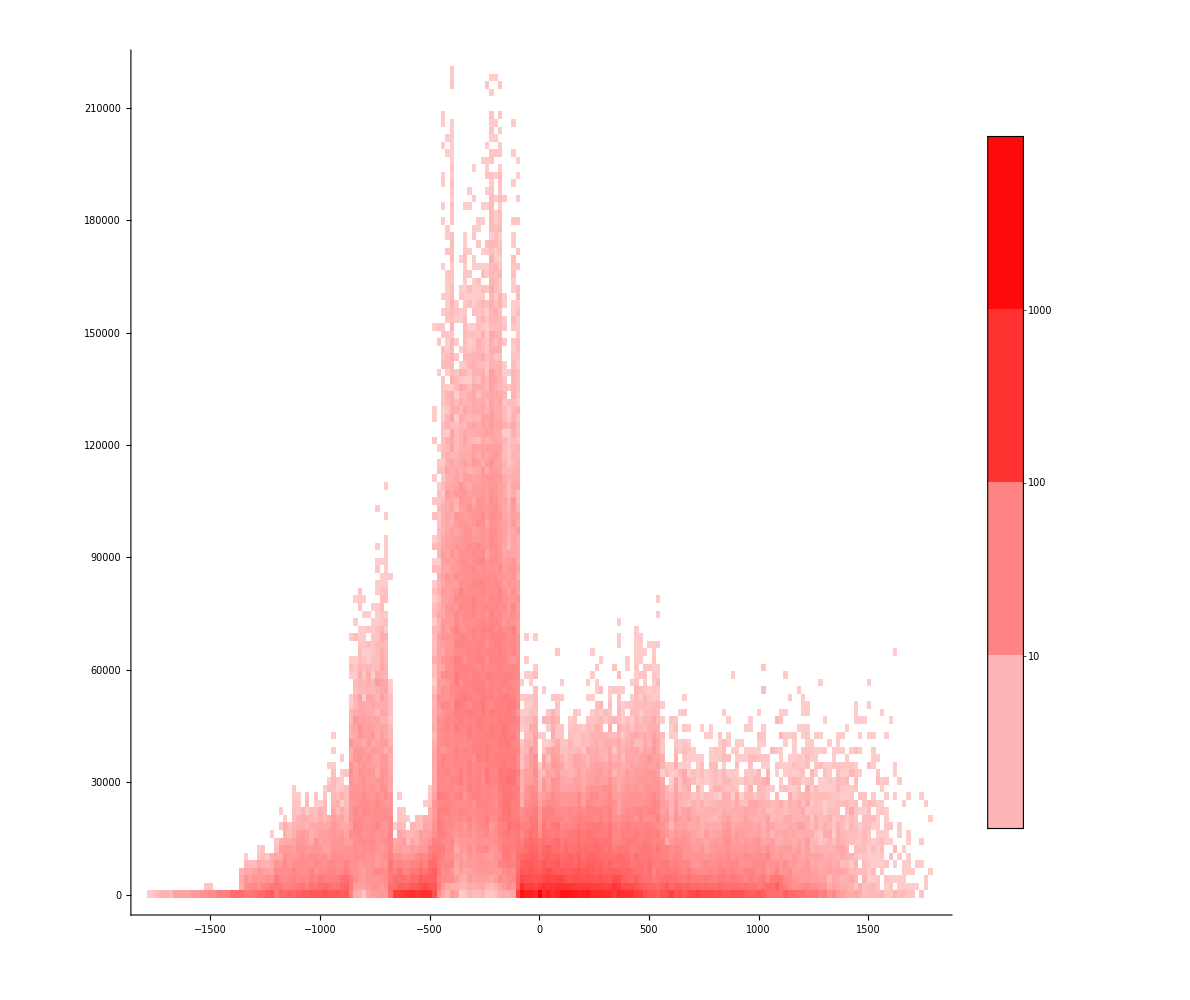

```mathematica
ArrayPlot[Apply[Hue,Transpose[Reverse/@Table[{1.,satfn[minsat,pxCquadrel[[lenY(i-1)+j]],maxquad],1},{i,lenX},{j,lenY}]],{2}],Frame->False,Axes->True,DataRange->{{-1780.,1800.},{0.,220000.}},AspectRatio->1,PlotLegends->BarLegend[{Hue[1,satfn[minsat,#,maxquad],1]&,{1,maxquad}},{1,10,100,1000,maxquad}],ImageSize->1000]
```

## Experiments with J_2 and J_3

## ML with polynomials

### Define network

Define a fully-connected feed forward neural network, L2Net, to be used for experiments with J_2 polynomial data. The function errorNet returns the list {relative errors over test sets for three runs of the network, data to plot it using functions defined in the section 'Plotting', trained network for further use if needed}. Training is run for 100 epochs with ADAM optimizer with variable learning rate.

```mathematica
L2Net=NetChain[{LinearLayer[100],ElementwiseLayer[Ramp],LinearLayer[300],ElementwiseLayer[Ramp],LinearLayer[300],ElementwiseLayer[Ramp],LinearLayer[150],ElementwiseLayer[Ramp],LinearLayer[75],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->48,"Output"->"Scalar"];
```

```mathematica
errorNet[data_,numruns_,epochs_]:=Module[{datasize=Length[data],relerrors,relerrmean,relerrlist={},sample,trainSet,valSet,testSet,results,trainedNet,vallosses,testPreds,plotdata,i},
Do[
sample=RandomSample[data];trainSet=sample[[1;;Floor[3/4 datasize]]];valSet=sample[[Floor[3/4 datasize]+1;;Floor[85/100 datasize]]];testSet=sample[[Floor[85/100 datasize]+1;;]];
results=NetTrain[L2Net,trainSet,All,ValidationSet->valSet,MaxTrainingRounds->epochs(*,TrainingStoppingCriterion-><|"Criterion"->"Loss","InitialPatience"->35|>*)];
{trainedNet,vallosses}=results[{"TrainedNet","ValidationLossList"}];
(*testSetMod=DeleteCases[DeleteCases[testSet,_->0.],_->0];*)
testPreds=trainedNet/@testSet[[;;,1]];
plotdata=Transpose[{testSet[[;;,2]],testPreds}];
relerrors=Abs/@(((testPreds)-testSet[[;;,2]])/testSet[[;;,2]])*100;
relerrmean=Mean[relerrors];AppendTo[relerrlist,relerrmean];
,{i,numruns}];
Return[{relerrlist,plotdata,trainedNet}]]
```

Note that in the following, I am only using fundamental polynomials for those knots for which we also know the adjoint polynomials.

### Fundamental up to 15

```mathematica
rule2upto15=MapThread[Rule,{jones2all,volsall}];
```

```mathematica
fundupto15=errorNet[rule2upto15,3,100];
```

```mathematica
plotdatafundupto15=fundupto15[[2]];
```

```mathematica
fundupto15[[1]]
```

{1.86192,1.86676,1.9018}

```mathematica
fundupto15[[1]]//Mean
```

1.87683

### Fundamental with 14 and 15

```mathematica
rule21415=MapThread[Rule,{jones21415,vols1415}];
```

```mathematica
fundw1415=errorNet[rule21415,1,100];
```

```mathematica
fundw1415[[1]]
```

{1.54764,1.54409,1.55156}

```mathematica
fundw1415[[1]]//Mean
```

1.54776

### Fundamental with 15

```mathematica
rule215=MapThread[Rule,{jones215,vols15}];
```

```mathematica
fundw15=errorNet[rule215,1,100];
```

```mathematica
fundw15[[1]]
```

{1.45548,1.49181,1.49199}

```mathematica
fundw15[[1]]//Mean
```

1.47976

### Adjoint up to 15

```mathematica
rule3upto15=MapThread[Rule,{jones3all,volsall}];
```

```mathematica
adjupto15=errorNet[rule3upto15,3,100];
```

```mathematica
adjupto15[[1]]
```

{0.49282,0.457009,0.51246}

```mathematica
adjupto15[[1]]//Mean
```

0.48743

```mathematica
adjupto15[[1]]
adjupto15[[1]]//Mean
```

{0.395565,0.416211,0.386789}

0.399522

```mathematica
plotdataadjupto15=adjupto15[[2]];
```

### Adjoint with 14 and 15

```mathematica
rule31415=MapThread[Rule,{jones31415,vols1415}];
```

```mathematica
adjw1415=errorNet[rule31415,1,100];
```

```mathematica
adjw1415[[1]]
```

{0.368873,0.374408,0.36284}

```mathematica
adjw1415[[1]]//Mean
```

0.368707

### Adjoint with 15

```mathematica
rule315=MapThread[Rule,{jones315,vols15}];
```

```mathematica
adjw15=errorNet[rule315,1,100];
```

```mathematica
adjw15[[1]]
```

{0.364433,0.330342,0.363666}

```mathematica
adjw15[[1]]//Mean
```

0.352814

## Saved plot data of ML predictions

We provide example data generated by an NN trained on J_3 polynomials. The relative error on the test set for this NN was 0.39%. This data can be used to run the pixelcounts function and generate a plot.

```mathematica
plotdataadjupto15=;
```

## Plotting the saved data from previous section

To plot the predictions of the neural network in an informative and appealing manner, we adopt the following strategy. The range of the axes is fixed by the maximum volume of knots in our database. We extend the range slightly, and consider both axes to go from 0 to 36. We then divide both axes into intervals of length 0.075, which in turn divides the image into square pixels. The function pixelcounts then counts the number of data points in the argument, plotdata, that fall into each pixel. The ratio of the count of points in each pixel to the maximum number of points in any pixel is used to determine a hue for each pixel. (This is the meaning of the legend, and explains why it ranges from 0 to 1.) The function plotfn2 converts the data for each pixel into a density plot.

### Functions for plotting

```mathematica
intervals=Table[{i,i+.075},{i,0,35.9,.075}];
pixels=Tuples[intervals,2];
numpixels=Length[pixels]
numintervals=Length[intervals]
```

229441

479

The argument 'plotdata' is a list of {volume of knot, prediction of volume by NN} generated by the function errorNet.

```mathematica
pixelcounts[plotdata_]:=
With[{xaxis=Sort@plotdata[[;;,1]],yaxis=plotdata[[;;,2]][[Ordering[plotdata[[;;,1]]]]]},
Module[{pixelCounts=Table[0,numpixels],i,j},
SetSharedVariable[pixelCounts];
ParallelMap[
Table[
If[intervals[[j,1]]<=yaxis[[#]]<intervals[[j,2]],
If[intervals[[i,1]]<=xaxis[[#]]<intervals[[i,2]],
pixelCounts[[numintervals(i-1)+j]]+=1
]
]
,{i,numintervals},{j,numintervals}
]&
,Range[Length[xaxis]]
];
UnsetShared[pixelCounts];
Return[pixelCounts]
]
]
```

```mathematica
huefn[huemin_,num_,max_]:=If[num==0,0,huemin*(1/huemin)^(num/max)]
```

```mathematica
hueArray[pxcounts_,huemin_]:=With[{max=Max[pxcounts],opac=1.},Apply[Hue,Transpose[Reverse/@Table[{1.,huefn[huemin,pxcounts[[numintervals(i-1)+j]],max],1,opac},{i,numintervals},{j,numintervals}]],{2}]]
```

```mathematica
fakevols=Table[{i,i},{i,0,35.75,.005}];
```

plotfn takes the plotdata argument explained above, along with a separate argument pxcounts generated using plotdata. This is because generating pxcounts is time-taking, and I preferred to generate and save the data for pxcounts first, and then use it to generate the plot if and when needed.

```mathematica
plotfn[plotdata_,pxcounts_,imSize_,label_,huemin_]:=ListPlot[fakevols,PlotRange->{{0,36},{0,36}},AspectRatio->1,ImageSize->imSize,PlotStyle->Directive[PointSize[.002],Opacity->.02],AxesLabel->{"Volumes","Predictions"},LabelStyle->Directive[FontSize->imSize/40,Black],Prolog->Inset[ArrayPlot[hueArray[pxcounts,huemin],PlotRangePadding->None,ImagePadding->None],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]],Epilog->Text[Style[label,imSize/40],Scaled[{.5,.9}]],PlotLegends->Placed[BarLegend[{Hue[1,huefn[huemin,#,1.],1]&,{0,1}},LegendMarkerSize->imSize/2],{1.,.5}]]
```

### Generating pixel counts

```mathematica
pxCadjupto15=pixelcounts[plotdataadjupto15];
```

```mathematica
(*DumpSave["pxCadjupto15.mx",pxCadjupto15];*)
```

### Loading data and plotting

```mathematica
J3upto15preds=plotfn[plotdataadjupto15,pxCadjupto15,1000,"J_3 up to 15 crossings",.35]
```

-Graphics-

## ML at evaluations (error vs phase)

In this section, we use evaluations of J_3 at multiple phases, and use these evaluations to train NNs with the objective of determining which phase leads to the best predictions. For functions here that are variants of functions used above, and the comments only talk about the differences.

### Evaluating J_3

```mathematica
phases=Join[Reverse[Table[1/(k+2),{k,0,7}]],Range[1/1000,499/1000,002/1000]];
```

```mathematica
nphases=Length[phases];
```

eval3atphaseprec evaluates J_3 polynomials at the given phase with the given precision. This is needed since there were problems at $MachinePrecision.

```mathematica
eval3atphaseprec[phase_,prec_]:=Chop[evalprec[#,phase,prec]]&/@jones3all
```

```mathematica
evalsJ3All=ParallelTable[{phases[[i]],evalatphaseprec[Exp[2π ⅈ phases[[i]]],35]},{i,nphases}];
```

```mathematica
evalsJ3sorted=evalsJ3All[[Ordering[evalsJ3All[[;;,1]]]]];
```

```mathematica
Monitor[reimevalsJ3=Table[ReIm/@evalsJ3sorted[[i]],{i,nphases}];,i]
```

### ML with J_3 evals

```mathematica
datasize=volsall//Length
```

177316

The neural network here takes as input the evaluation of J_3 of a given knot as the list {real,imaginary} containing real and imaginary parts. We checked that taking the list {abs,argument} does not change the results significantly.

```mathematica
L2NetPhase=NetChain[{LinearLayer[50],ElementwiseLayer[Ramp],LinearLayer[75],ElementwiseLayer[Ramp],LinearLayer[75],ElementwiseLayer[Ramp],LinearLayer[50],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->2,"Output"->"Scalar"];
```

```mathematica
relerrorPhase[data_,numruns_,epochs_]:=Module[{relerrors,relerrmean,relerrlist={},sample,trainSet,valSet,testSet,results,trainedNet,vallosses,testSetMod,i},
Do[
sample=RandomSample[data];
trainSet=sample[[1;;Floor[3/4 datasize]]];
valSet=sample[[Floor[3/4 datasize]+1;;Floor[85/100 datasize]]];
testSet=sample[[Floor[85/100 datasize]+1;;]];
results=NetTrain[L2NetPhase,trainSet,All,ValidationSet->valSet,MaxTrainingRounds->epochs,TrainingStoppingCriterion-><|"Criterion"->"Loss","InitialPatience"->25|>];
{trainedNet,vallosses}=results[{"TrainedNet","ValidationLossList"}];
testSetMod=DeleteCases[DeleteCases[testSet,_->0.],_->0];
relerrors=Abs/@(((trainedNet/@testSetMod[[;;,1]])-testSetMod[[;;,2]])/testSetMod[[;;,2]])*100;
relerrmean=Mean[relerrors];
AppendTo[relerrlist,relerrmean];
,{i,numruns}];
Return[relerrlist//Mean]]
```

```mathematica
rule3reim=Thread[Rule[#,volsall]]&/@reimevalsJ3[[;;,2]];
```

```mathematica
Monitor[errsJ3=Table[relerrorPhase[rule3reim[[i]],3,50],{i,258}];,i];
```

### Results and plot

```mathematica
errsJ3={13.048590187659373,12.97150176713872,12.973915786835882,12.610037108663526,12.71768479257888,12.857059284928326,12.823413792553845,12.93471318539278,13.030700954637767,13.025202727501792,13.282740967244642,13.273293931852686,13.42612871992399,13.439329094843375,13.478258703370534,13.651717170008313,13.70632557456011,13.8303688955868,13.775115795907553,13.781955612437704,13.924520975499432,13.91266858246693,14.003035199149743,13.992171873520403,14.068235665709638,13.993742993699906,14.04583243080567,14.056845342847744,13.954662583672658,13.96238693344599,14.0187853628073,14.063746614979982,14.106734045470821,14.125364877097317,14.08620632929428,14.086661449554967,14.105189533373688,13.958739759593747,14.01717552035223,14.150217700959844,14.173034689676138,14.110037268456907,14.179445237797866,14.114650114563531,14.008080399494483,14.10360806807158,14.072737641323215,14.121063866727802,14.26973682828587,14.207435415256441,14.02986651595797,13.923391996802609,14.085481003591559,14.158789440575328,14.150687668768507,14.165524798626492,14.057926656556942,14.129107407429244,14.178522614259416,14.123614024800565,13.97727653337279,14.154029392914552,13.94716720182918,14.104188531264683,13.885787216734045,14.069816880197621,14.16384308634268,14.08927749452234,14.125782083366934,14.114656083659604,14.027091751001416,14.106039984422813,14.126382444547048,14.166875060532895,14.14038875788245,14.101952866304174,14.105853600398575,14.066295418977916,14.121554967790047,14.04677235347598,14.02713342061189,14.001745279599916,13.918240728319388,13.780076695670685,13.836216282772781,13.611363707442086,14.008305546490694,13.486068539660314,13.612955416108775,13.492105733375618,13.273253747836113,13.120979446707304,13.06057024060246,12.892136298991234,12.655363105317415,12.576282547105167,12.318383060808088,12.19477630968282,11.967805844853869,11.898049566555523,11.559636363011217,11.4003937269674,11.171882008439992,11.412852827162823,14.093794480315617,11.509987479077282,10.422999899085488,10.060301775321498,9.699558143592322,9.303148061345984,8.951019995909512,8.689268015624284,8.36673892441288,8.014192885581954,7.648344368647341,7.357484551260612,6.956859784343442,6.643234768284123,6.286153692279175,5.973080601031785,5.6063267996789605,5.264875976534909,4.950126616713952,4.619130477495778,4.294356261958583,4.007197245010011,3.718156567243531,3.4068821357153376,3.144145654948805,2.88598296186682,13.880454548901499,2.637450424061296,2.3018135375511015,2.023477446748884,1.801616554502857,1.6055343423559234,1.4275191908954152,1.2678396005785022,1.1801180828466513,1.2297778535278203,1.393819631602222,3.3155673587113434,1.9093034336959347,2.1064954959864934,6.004618285573645,2.324217447229964,5.413573179112856,5.351750696496251,4.252154111564201,4.540397508453466,4.386431285828813,5.9481184145428685,8.059843706030074,8.56894669313037,10.894317056732385,6.142052555988776,6.076513196635616,5.202191029928657,5.942467880694217,12.19776752318171,7.365852645619301,8.83278110230914,8.59684592736526,6.144518682083099,8.155094386033776,13.974605211966255,10.2495236136642,7.19928079339737,7.85022933757845,8.054385543665319,7.781916435698739,6.587033364037677,8.647450868361096,8.042505043805606,10.704720398695244,9.86430350648927,7.3561152909810055,10.457185879893375,9.445679697811755,10.4192142177331,7.749872044322438,9.457772973331744,6.979032209638382,7.290090566893862,7.26878240058534,6.831536659598982,6.910338871734756,7.343198689380965,6.836470719833677,7.079141497653548,6.79377737060539,6.96710659499999,7.053581759172025,6.9405977960191025,7.3683629099878445,7.000191882738204,7.071557034782973,6.927282534920536,6.869428454818483,6.566845119930292,6.425215997263567,6.088907294910816,5.726306256311376,5.206811285711217,4.697338750217142,4.16520195042983,3.7875707460166956,3.6252017023724386,4.282753429754043,5.67574442515203,7.17594084654333,8.471621344998518,9.359925601345948,10.078186715187528,10.670249552105517,11.334554922531671,11.833897444433054,12.431056178525077,12.866831083950428,13.20959889467114,13.62215631362473,13.698554916149895,13.809090060753453,13.916974219092536,13.950505807959281,13.933925955569583,14.09240523906581,13.908551387957301,13.938493725188911,14.017119039157203,13.885717181320054,13.923204423650708,13.872048768266401,13.882588932697416,13.770890779870252,13.895345502611057,13.8772099442397,13.89114531939221,13.842669427172893,13.896221152406858,13.858691442018376,13.860388431856398,13.913478785846936,13.925075479214021,13.767394889628909,13.80768133412554,13.670839790896848,13.674821695723077,13.551414464940187,13.637183151596878,13.382585676834152,13.206606040463244,13.09267558335158,12.858723781089116,12.7254800392921,12.857016355441493,13.02748956795302,13.920948312210541};
```

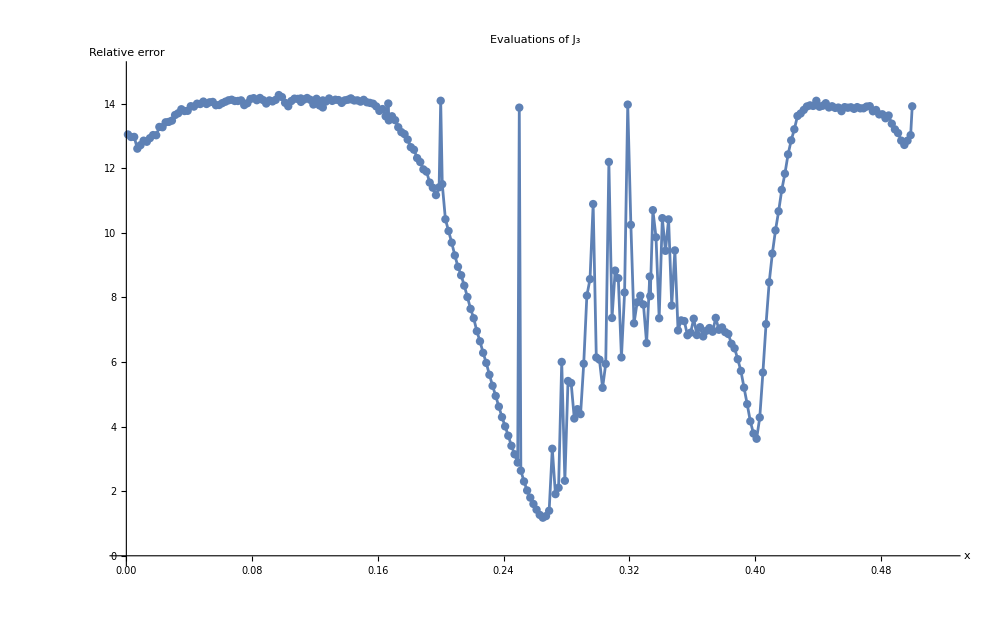

```mathematica
plotall=ListPlot[Transpose[{Sort[phases],errsJ3}],PlotRange->{{0,.52},{0,15}},AxesLabel->{"x","Relative error"},PlotLabel->"Evaluations of J_3",LabelStyle->Directive[FontSize->20,Black],AxesOrigin->{0,0},Joined->True,ImageSize->1000,Mesh->All,PlotStyle->Directive[col1,AbsolutePointSize[6]]]
```

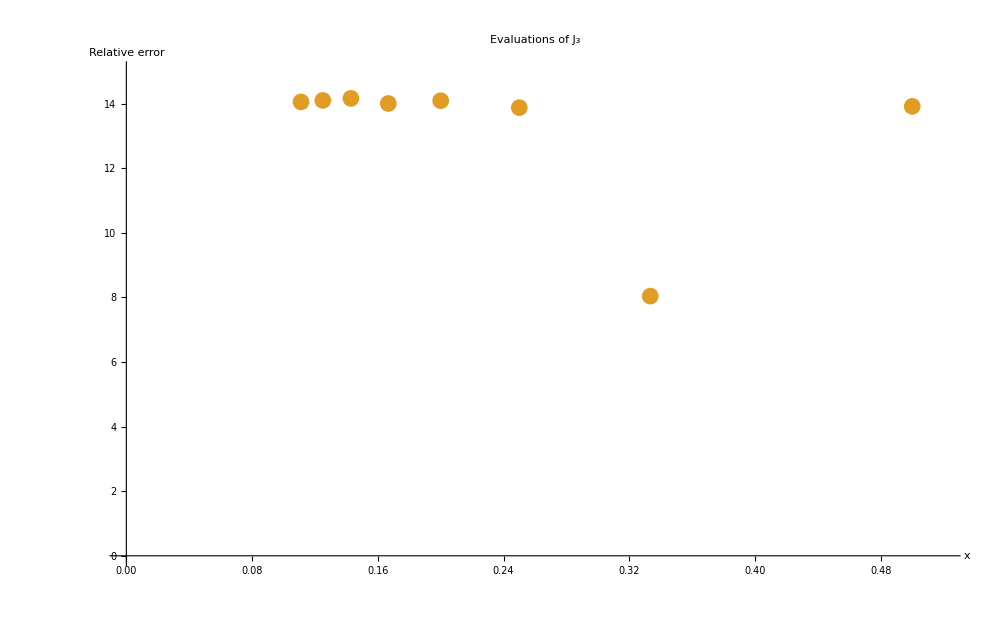

```mathematica
plotint=ListPlot[Transpose[{Reverse[Table[1/(k+2),{k,0,7}]],Extract[errsJ3,(Position[Sort[phases],#]&/@Reverse[Table[1/(k+2),{k,0,7}]])[[;;,1]]]}],PlotRange->{{0,.52},{0,15}},AxesLabel->{"x","Relative error"},PlotLabel->"Evaluations of J_3",LabelStyle->Directive[FontSize->20,Black],AxesOrigin->{0,0},ImageSize->1000,PlotStyle->Directive[col2,AbsolutePointSize[12]]]
```

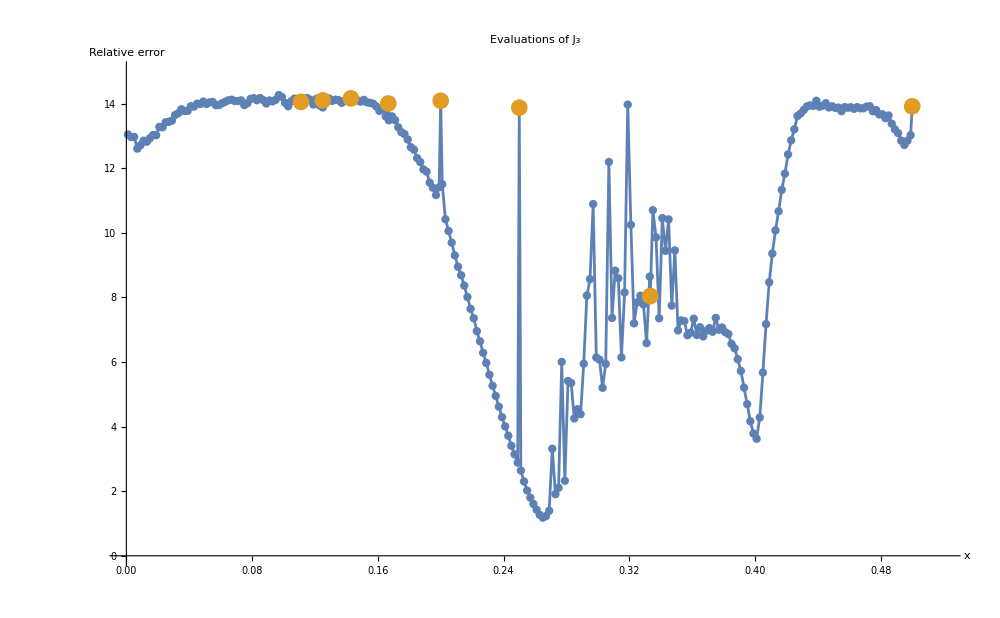

```mathematica
plotJ3joined=Show[plotall,plotint]
```

## ML at evaluations off the circle

Here we try to check if evaluations away from the unit circle can be used to predict volumes meaningfully using NNs.

```mathematica
L2NetPhase=NetChain[{LinearLayer[50],ElementwiseLayer[Ramp],LinearLayer[75],ElementwiseLayer[Ramp],LinearLayer[75],ElementwiseLayer[Ramp],LinearLayer[50],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->2,"Output"->"Scalar"];
```

```mathematica
relerrorPhase[data_,numruns_,epochs_]:=Module[{datasize=Length[data],relerrors,relerrmean,relerrlist={},sample,trainSet,valSet,testSet,results,trainedNet,vallosses,testPreds,plotdata,i},
Do[
sample=RandomSample[data];trainSet=sample[[1;;Floor[3/4 datasize]]];valSet=sample[[Floor[3/4 datasize]+1;;Floor[85/100 datasize]]];testSet=sample[[Floor[85/100 datasize]+1;;]];
results=NetTrain[L2NetPhase,trainSet,All,ValidationSet->valSet,MaxTrainingRounds->epochs];
{trainedNet,vallosses}=results[{"TrainedNet","ValidationLossList"}];
testPreds=trainedNet/@testSet[[;;,1]];
plotdata=Transpose[{testSet[[;;,2]],testPreds}];
relerrors=Abs/@(((testPreds)-testSet[[;;,2]])/testSet[[;;,2]])*100;
relerrmean=Mean[relerrors];AppendTo[relerrlist,relerrmean];
,{i,numruns}];
Return[relerrlist]]
```

```mathematica
points1=Table[r E^(8.π ⅈ/15),{r,.85,1.15,.05}];
points2=Table[r E^(802.π ⅈ/1000),{r,.85,1.15,.05}];
```

```mathematica
evalspoints1=eval3atphaseprec[#,30]&/@points1;
evalspoints2=eval3atphaseprec[#,30]&/@points2;
```

```mathematica
rulespoints1=Thread[Rule[ReIm[#],volsall]]&/@evalspoints1;
rulespoints2=Thread[Rule[ReIm[#],volsall]]&/@evalspoints2;
```

```mathematica
relerrorPhase[#,1,25]&/@rulespoints1
```

{{75965.7},{17.026},{9.5549},{1.1672},{9.60857},{13.9386},{24.3325}}

```mathematica
errorResults1=Flatten[{{75965.65683799883},{17.026047063502784},{9.554899113234361},{1.1672043508932723},{9.608571054552561},{13.93858773319208},{24.332518073053652}}]
```

{75965.7,17.026,9.5549,1.1672,9.60857,13.9386,24.3325}

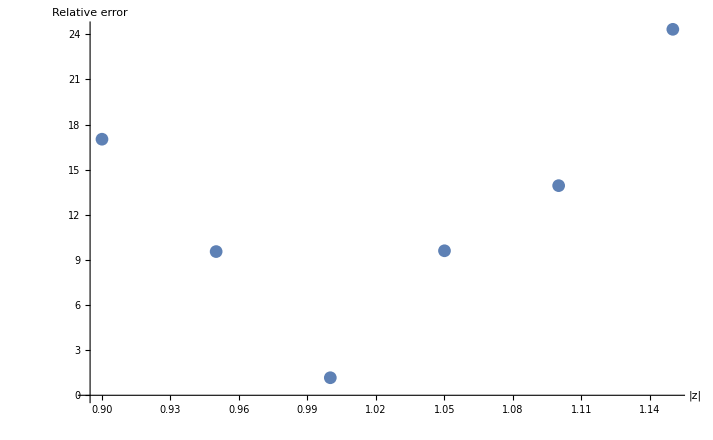

```mathematica
ListPlot[Thread[List[Abs[points1][[2;;]],errorResults1[[2;;]]]],AxesLabel->{"|z|","Relative error"},LabelStyle->Directive[FontSize->15,Black]]
```

```mathematica
relerrorPhase[#,1,25]&/@rulespoints2
```

{{11213.},{111.728},{11.2684},{3.56182},{11.7904},{13.3926},{25.5704}}

```mathematica
errorResults2={{11213.041626320188},{111.72788587280614},{11.26835825268081},{3.561823918350341},{11.79041670144906},{13.392643254013562},{25.570418511267277}}//Flatten
```

{11213.,111.728,11.2684,3.56182,11.7904,13.3926,25.5704}

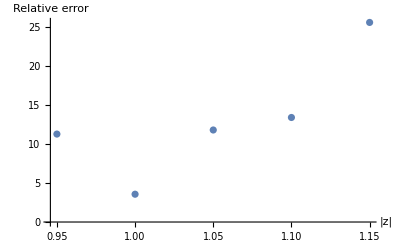

```mathematica
ListPlot[Thread[List[Abs[points2][[3;;]],errorResults2[[3;;]]]],AxesLabel->{"|z|","Relative error"}]
```

## Fitting using evaluations — symbolic formula

### Fitting

Evaluate J_3 at the relevant best phase, and save the data for reuse.

```mathematica
eval3at4by15=Abs[eval3atphaseprec[E^(8.`50π ⅈ/15),40]];
```

```mathematica
nlmdata4by15=Transpose[{Abs[eval3at4by15],volsall}];
```

```mathematica
nlm2=NonlinearModelFit[SetPrecision[nlmdata4by15,20],a Log[x+b]+c,{a,b,c},x,Method->{"Newton", "StepControl"->{"LineSearch",Method->"Brent"}},WorkingPrecision->20,MaxIterations->1000];
```

```mathematica
nlm2["BestFit",WorkingPrecision->10]
```

-1.72473261+3.252986946 Log[36.97068599+x]

```mathematica
Grid[Transpose[{#,nlm2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

AdjustedRSquared | 0.9996251070670735922
AIC | 208831.7847283809
BIC | 208872.12748330297
RSquared | 0.9996251134098672418

```mathematica
nlm2[x_]:=-1.725+3.253Log[x+36.971]
```

### Generating pixel counts

These are commands to generate the plot in the next subsection.

```mathematica
sample1pos=RandomSample[Range[datasize],5000];
sample2pos=RandomSample[Complement[Range[datasize],sample1pos],5000];
sample3pos=RandomSample[Complement[Range[datasize],sample1pos,sample2pos],5000];
sample4pos=RandomSample[Complement[Range[datasize],sample1pos,sample2pos,sample3pos],5000];
sample5pos=RandomSample[Complement[Range[datasize],sample1pos,sample2pos,sample3pos,sample4pos],5000];
```

```mathematica
sample1=eval3at4by15[[sample1pos]];
sample2=eval3at4by15[[sample2pos]];
sample3=eval3at4by15[[sample3pos]];
sample4=eval3at4by15[[sample4pos]];
sample5=eval3at4by15[[sample5pos]];
```

```mathematica
nlm2eval1=nlm2/@sample1;
nlm2eval2=nlm2/@sample2;
nlm2eval3=nlm2/@sample3;
nlm2eval4=nlm2/@sample4;
nlm2eval5=nlm2/@sample5;
```

```mathematica
plotdataNLM1=Transpose[{volsall[[sample1pos]],nlm2eval1}];
plotdataNLM2=Transpose[{volsall[[sample2pos]],nlm2eval2}];
plotdataNLM3=Transpose[{volsall[[sample3pos]],nlm2eval3}];
plotdataNLM4=Transpose[{volsall[[sample4pos]],nlm2eval4}];
plotdataNLM5=Transpose[{volsall[[sample5pos]],nlm2eval5}];
```

```mathematica
pxCNLM1=pixelcounts[plotdataNLM1]
```

```mathematica
pxCNLM2=pixelcounts[plotdataNLM2]
```

```mathematica
pxCNLM3=pixelcounts[plotdataNLM3]
```

```mathematica
pxCNLM4=pixelcounts[plotdataNLM4]
```

```mathematica
pxCNLM5=pixelcounts[plotdataNLM5]
```

```mathematica
pxCNLM=pxCNLM1+pxCNLM2+pxCNLM3+pxCNLM4+pxCNLM5;
```

```mathematica
(*DumpSave["dataFiles/pxCNLM.mx",pxCNLM];*)
```

### Plotting

```mathematica
plotdataNLM=Join[plotdataNLM1,plotdataNLM2,plotdataNLM3,plotdataNLM4,plotdataNLM5];
```

```mathematica
NLM1preds=plotfn[plotdataNLM,pxCNLM,1000,"Predictions from fit",.35]
```

-Graphics-

## Checking the guess

```mathematica
volK0=3.474247;
vol41=2.02988321282;
```

```mathematica
guess[n_]:=(2π ⅈ)/((n^2-2)/(n+1)+2)
```

```mathematica
guess/@{2,3}
```

{(3 ⅈ π)/4,(8 ⅈ π)/15}

### K_0

The q-functions in this subsection are written in terms of b where q = b^2.

```mathematica
qintbEx[b_,n_]:=qintbEx[b,n]=((b^n-b^-n)/(b-b^-1))
qfacbEx[b_,n_]:=qfacbEx[b,n]=If[n==0,1,(qintbEx[b,n]qfacbEx[b,n-1])]
qbinombEx[b_,n_,k_]:=qbinombEx[b,n,k]=(qfacbEx[b,n]/(qfacbEx[b,k]qfacbEx[b,n-k]))
```

```mathematica
qfac2bEx[b_,n_,k_]:=If[n==k,1,qintbEx[b,n]qfac2bEx[b,n-1,k]]
```

```mathematica
ZbEx[b_,n_,k_,l_]:=Sum[(-1)^(k/2+z)qbinombEx[b,(k+l-n)/2,(n+2k+l)/2-z]qbinombEx[b,(n+l-k)/2,(3n+l)/2-z]qbinombEx[b,(n+k-l)/2,n+k-z]qfac2bEx[b,(2n-k)/2,z-(n+k+l)/2]qfac2bEx[b,z+1,(n+k+l)/2+1],{z,Ceiling@Max[(2n+k)/2,(n+k+l)/2],Floor[Min[(n+2k+l)/2,(3n+l)/2,n+k]]}]
```

```mathematica
JK0altb[b_,n_]:=JK0altb[b,n]=1/qintb[b,n+1] Sum[Sum[b^(-3/4(2k+k^2)+7/4(2l+l^2)-51/4(2n+n^2))(qintb[b,k+1]qintb[b,l+1])/qfac2b[b,n+k/2+1,k/2] qfacb[b,k/2]Zb[b,n,k,l],{l,Abs[n-k],n+k,2}],{k,0,2n,2}]
```

The above is the n+1-dimensional colored Jones polynomial for the knot K_0, given in equation (5) of arxiv:math/0412331.

Generating jk0list takes a bit of time.

```mathematica
Monitor[jk0list=Table[JK0altb[b,n],{n,1,50}];,n]
```

```mathematica
DumpSave["jk0listraw.mx",jk0list];
```

Generate and store data for volumes obtained from the volume conjecture.

```mathematica
b0[n_]:=Exp[(π ⅈ)/(n+1.)]
```

```mathematica
vcnumerator=Table[2π Re[Log[SetPrecision[SetPrecision[jk0list[[i]],100]/.b->SetPrecision[b0[i],100],100]]],{i,50}];
```

```mathematica
vcnumerator={10.1123966442237253639787153040470614880712668542785257634788798696080358089845098678491672383733994533122493950964168`100.35718922532311,-3.040792849547460160740531672858844649464963601266263632504787252998005448990324612506450991388815168795`86.83532196482261*^-13,19.5550270332519278888933583776492241019017663297398442116509471997028637885912867024126400499001168661680410439947396`100.64359355013963,26.8518375772724518491199371017221147372955510522193637651012614283873670257851519986190800359189680631346944291133939`100.78130914101268,27.0961448511518550607235918715015478763414573534621801055925439739636713155356229893359619422983902191790447672564288`100.7852426347774,35.922950274288909575902266259516705358157131735711300738347075588713906313025240888726170260346915180810306570570541`100.90770712660131,43.0774348010285366645600439344197062600736163526124339453422012624585513613449891358844268945047045494643699776827714`100.98658496326121,46.904340865949902033703733830273460700318009584621177975648024158089965527597123918583240671795718387455790035998366`101.02354816679215,49.7475833131754249147945055277083011189574102885753383285214102565100491917507496100403959425465761074062962106171461`101.04910711748536,54.697929814720044244775819194677342371716277179700817304721567113460269230483940001067290291936254548148842493571228`101.0903060191152,59.8854929461576669581424157611779346908683297888395682586747131893967024172420660646728009763564881850649898188727504`101.12965675826572,63.8907358866967075442299411124362271584439619192837987188073042515811545528909457598718585731414740798175610937127389`101.15777301979244,67.4266551430860853083720295574134645870023521964580513828924919362109962729425705609013288120182038679049302980061777`101.18116674549147,71.6313693974137549309581364045209832996517552616893585676917952216827303503589470716615323846636447661072913187171677`101.20743838324393,76.0697653944416770262073117557708858489223042242665056887471110548400453946657749452978709832097420988758961778570183`101.23354720633021,80.0393038988236206214871492101542619963356832104654004747999364274091850555455715575858333876999384172815169349818663`101.25563843239888,83.7942233790191578392895002968438623048911327032112497308328716629519452558816914893554542438596020801530020709876168`101.27554920966634,87.7926046274907795759217298506998413411982237146991493449416104509264485983532764527693398201568722843395504408216933`101.2957930633214,91.8873397728151098805192956483612886579895796440164335016643830138993106390309799518675106808965805176267703427117997`101.31559080793764,95.7975673861265340144985449864036074293343643196979982283601433459336002566921490000109404364458997712624682933346984`101.33368961053368,99.6070175661971562899438842816350786733318949123772815404062390711763066465921794135778103793685810831187491905780972`101.3506250661196,103.4949304118204833428013585818902509821759432559416385706350903778183160559369791869170789051290841376734128506494297`101.36725420633833,107.4196178105585638870189782459407087440430242172862619650806454420162712863251976371982463310908551826558775264389378`101.38341873233497,111.2704518675067516449830986929048384617009539941435465329643830559639609805731381587712112118132229414619845528616868`101.3987149811886,115.0713406631601464519915614727842814929100772580577091829146216247646101049679590424257396935012792052864562867075829`101.41330230243751,118.8933923467041236878149447315107422614935942884442042131213547538128939763120709357105323771027584345488605656441418`101.42749284828847,122.7262889432893460212612558711780243095265491715764529538768637868148181352844616562010946364011600234452338243358635`101.44127273148446,126.5269860263809420942837587101782728092839958317014575983679463032062773698790894581871235717439875086735846093092812`101.45451829239623,130.3017164905234018555595129295038108030130487762895346382237722063790590108103229699644635005685105476128895216246322`101.46728526627204,134.0784726591078450029411654281530151976375940378708268063767104591113986833067747413307192203792545735586148723931368`101.4796941835681,137.8555728152758885791153828133798750953629684007451289896060202561060480250419239019179570632866341472294483120418906`101.49175945663674,141.6165942477450925368244940205463873611211329505069617453999350589361537503384588375142107694116213539080253493822641`101.50344927525681,145.3628749822954570542601232269234174519169447884378197115721718322876687260551829372556268426804658871252871101499671`101.51478863332116,149.1054246173992252784294638321996706358410228778117334944642378153850671380368352467516635616585450942725605688866413`101.52582857331953,152.84458493716624370874841202233281194400438188534107492098003683954350634563409521698536775644751859550662604917705`101.53658518638245,156.5742367498870616946748442792623032088663773921572547615900378034102782829972637596452830619390373429779862138314708`101.54705543280349,160.2945709819420081739766427670743800051080749989571683742790583626023140499458838248553553373821482607059972153176714`101.55725394295396,164.0099558594256539656797766005867073054157909480454562754495954526855844664379352929301034493433707635275442232703327`101.5672053412019,167.7209741323514407733677854296146811582303534059613598189788488503468395389190074493637930974491122372476620833186716`101.57692250561821,171.4254401585500202561235005668377731042561570303812255730938596806397356777338432225443959853514072728296139571014034`101.58641040272393,175.1233707008558605635398840355390529646874770521689789405613989754772588266816821754198214048381352792652085217066051`101.59567923723141,178.8165435667473923310511745924156705086719304811910534123472177968726297686400800517253785896222011840005083926586918`101.60474282540682,182.50541218943924894270146700860335850875849784523894754864998984353868207062210927872724685804131025700063380261529`101.61361087743983,186.1892637538792309568703235310374115104150580127258923283679439642594072755989940221331130451266399047125380570273832`101.6222897640844,189.8681361197267806627022486416070607341885123188882913123878801931696634828252259966124284167458174569443096127094248`101.6307872165464,193.5427939811236632947954890833048815459888706705725520554485266345392734104228120635654264613529177296531106299951291`101.63911213570238,197.2135449127625818989003029162826658192122654174566562072726695719141037367082053078131335650385705527787102429887318`101.64727186907936,200.8802109515829029031992302050431927583070683085059656302265718674985035125009652915629196164363482715730777836596444`101.65527228524735,204.5428612091132538995815445081557638076454360393864424172835177268598703386078511039291809276586139570411548357952237`101.66311945617508,208.2018583954824953379520036253565100922866857173300932650474427298516058604244087579392160204784666368645062428964114`101.6708197311484};
```

```mathematica
vcplotdata=Thread[List[Range[2,51],Chop[vcnumerator/Table[i+1,{i,50}]]]];
```

Generate and store data for volumes using our guess for the best phase.

```mathematica
guess[n_]:=(2π ⅈ)/((n^2-2)/(n+1)+2)
bguess[n_]:=Exp[(π ⅈ)/((n^2-2)/(n+1)+2)]
guessnumerator=Table[2π Re[Log[SetPrecision[SetPrecision[jk0list[[i]],100]/.b->SetPrecision[bguess[i+1],100],100]]],{i,50}];
```

```mathematica
guessnumerator={7.9739870374976905892339591368181953241496430951934332199754367568041032619215222015069633296756248868997298573572502`100.25401065481232,8.4060796069414791411889376137142003117146225163810356015092766581897399567479763411386628456068909314782677325895335`100.27692862800217,15.0712631986188430189655980996042022215476930627624517486963577606042410120857821117970187787667767547177091843024497`100.53048478372604,21.6713551777742315066151972470906399565116937939879743006399970195534839045540203366665978864629352335114379257592796`100.68822119943823,24.643604905983911768724587056877364062199096702835590467541848662486560318275389919324913458680602709413022585846899`100.74403936690547,26.1095306167420333192126885589055044628177445689125752718320684873423617880345411961115029401238213227467067079607344`100.76913419385173,30.7137442346847170179949497327631381360582881937759869804785043838507718385352508919579607287172002833089198234200048`100.83966789288345,36.0757863193691318679133675365688636921441362427529388770508656044036382702796401290984455372856048142618651144601236`100.90955093536388,39.638634515327143086808171472537218780018960383384245987175248140930415735965736523276619417663608572568356288854919`100.95045381482616,42.2738155116684591081187995665165583153100696080551910210939383612812566095419694775342970155744186547068101881897899`100.9784065772291,46.2082022267497492380988345859940516022364612281175851140771113427238405605814854397054078297923141814071576331481131`101.01705420168895,50.644531119900041785934268764382943543542009177890397251989825362440950931739562666820652572958026894977512041254405`101.05686768415174,54.2768101738878842094047878846243863146309604256864019939459921391585043241480813314017948967443103794634960251346923`101.08694944590104,57.5591899770217233517437143856451221033679866761800149165962071298527904903099695397240209292527526960939013506393288`101.1124498030118,61.2872033526963495950653872224581702091513985726212019292885452739259872346431962760490000923058874168984544986672285`101.13970493362574,65.2175863983297004074046843985029416076433729199366878776069158162567171678940857540576684344778482911397415674514738`101.16669985167636,68.8632677307465964333343164192348252712713655837790174663623344947097112776527232948023242842167186336887155528286992`101.19032275666854,72.3559508078209958160383705298241118688778154236754097980876814974357154812394955951026228160244621094097649402007854`101.2118093843031,76.0023609558825901828766710723284985800780762050229084870555987058742870870641760417182796295567332534439570999743434`101.23316221299396,79.7345574704143004041359742175420968248393111829360487329983717750160866782618565341644577484471543496684511038511001`101.25398171769473,83.3606993215480966131407609041325399565366029030427286240825410174835261192321501918241485076520422353067352894518982`101.27329647878604,86.9193161122827880028091376773493792962736282253502502626120767141042724056254951136892095664251062732994896096149627`101.29145143007413,90.5302109699521581380446947854089624324512361115912973837194142188843851276975388526144955342528664342597951900639201`101.30912866191748,94.1749088964660543538692600550987377742926722717988078165557446837955507734899890254787639000937472217765324816898951`101.32627033821876,97.7794252133773212558971960109418121025134821784876829061733726964640281323331253450546970900855847539690140568657312`101.3425826094523,101.353557612527233217807818376785231835794436845791001219701028860379156304918724918635624473078161060724396524797093`101.35817412694664,104.9436780850909766274010775397482699726350986229321843640258942595899227159085840129861456979928199944223771921221291`101.37329141083482,108.5460724326201998143077358795847145583442184019175331924073045871073598893388654792091399315144139504552027203516717`101.38794924329196,112.132407831251483626260959748003975539887471149354312761980816263299477938868036597964280013337593576447366907077604`101.40206627737855,115.7044745538848682038301486159145843606668335818797718111583074421128444996462223658031761039584601332360455214167062`101.41568528390087,119.2801867051576689516467918087096683243434438023133401856486996491857564613010429383008874111584306367152974495784775`101.4289034397055,122.8594667779183601466331479789695911596192166529611528229279437316442614405283647960114602429477835728485002529637438`101.44174375558106,126.4315713029690771066039395840525533637132174849926500137030130258686896868058329691547506068139497507363086421415206`101.45419066489653,129.9964771765421857391127686110733927580568972933672814674448966219430082494965163192791005041447995925994350313411385`101.46626671283057,133.5610836942755615003713965770644174793227211390779889602643004854577276598802333851244238117568637116413134337409997`101.47801506366973,137.1259115766919460933886364242933587249881931357508240365900884823525778652140906810883777935827785596152001572009729`101.48945465714077,140.6869499804131725868882831169018634934171118711967214513467397769507021076455930707811317688600919281185380432743556`101.5005889439353,144.243947412462452285914463964331873804716019620870391970157148031819660391191551346171603797418934628784785312239621`101.51143272835179,147.7995668305734265773541075558861830272205433868160686384161117460371667050049816778056327377399291394216181697920704`101.52200829070881,151.3542434117624364282583392195283570176027585004324939297029602971130098567739577160969932371587064502604835640949517`101.53232973094404,154.9065168009148113385291784457957827694360708235207573201381435712622527262694161781524818944024525544552305422263513`101.54240481806033,158.4562215098681397171392720467547287649952160702103825568117742537364273332750913066849422522608957058605424815567603`101.55224442515772,162.0043983537453792829163930076145773677193729095180431043251320797489377685586195172891542092817622349380960924038781`101.5618619350957,165.5513230744275306975806112412735546815852492449195201541748349392959260499042864920854735538038374317152634753365742`101.57126778542651,169.0964890395920091380989823094291571853713936380393508460885283865929829468271033345091594355857232686834668662125014`101.5804697198832,172.6398251014361794298081561767835841011459455887890331520506327247121885047825079496583290875109245541057321188579934`101.58947611683634,176.1817516234221098876463407617920541260187460490385223597610991070446853613319146635547138847931456456193086318763105`101.59829605296154,179.7224312087567913122017876139979824945871999057693178004669574633871709667357597161786195644749020772822519110514158`101.606937414386,183.2617069408045769926120560906590889221852916549530882398727479717715464181766520896735294272659773563186776071663304`101.6154068568383,186.7995634272424538699076325258853502911572435100371583357883254809394596034293303424904422685940862769965043675208517`101.62371098637136};
```

```mathematica
guessplotdata=Thread[List[Range[2,51],Chop[guessnumerator/Table[i+1,{i,50}]]]];
```

```mathematica
volK0plot=Table[{i+1,volK0},{i,50}];
```

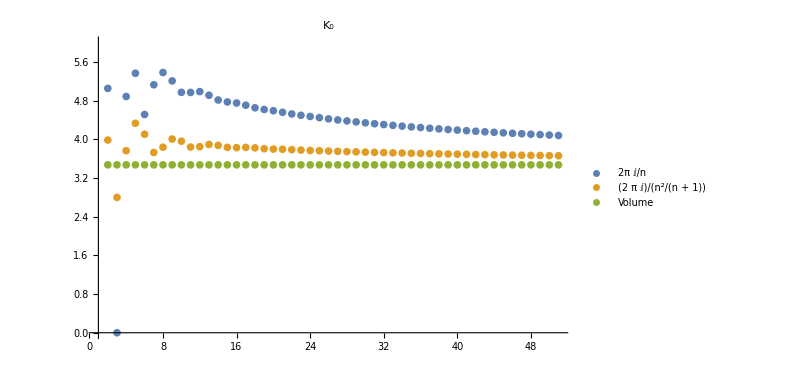

```mathematica
imgK0=ListPlot[{vcplotdata,guessplotdata,volK0plot},PlotRange->{All,{0,6}},PlotLabel->"K_0",LabelStyle->Directive[FontSize->15,Black],PlotLegends->Placed[{"2π ⅈ/n","(2  π ⅈ)/(n^2/(n + 1))","Volume"},{.8,.4}],ImageSize->600]
```

```mathematica
Export["imgK0.png",imgK0]
```

imgK0.png

### 4_1

```mathematica
qint[q_,n_]:=qint[q,n]=((q^(n/2)-q^(-n/2))/(q^(1/2)-q^(-1/2)))
qfac[q_,n_]:=qfac[q,n]=If[n==0,1,(qint[q,n]qfac[q,n-1])]
qbinom[q_,n_,k_]:=qbinom[q,n,k]=(qfac[q,n]/(qfac[q,k]qfac[q,n-k]))
```

```mathematica
qg[n_]:=qg[n]=Exp[(2 ⅈ (1+n) π)/(n (2+n))]
```

This is the n-dimensional colored Jones polynomial for 4_1 given in equation (2.2) in arxiv:2209.07751.

```mathematica
Jn41Mur[q_,n_]:=Sum[q^(-n k)Product[(1-q^(n+l))(1-q^(n-l)),{l,1,k}],{k,0,n}]
```

```mathematica
evals41=2π Abs[N[Table[Log[Jn41Mur[Exp[(2π ⅈ)/n],n]]/n,{n,2,100}],50]];
```

```mathematica
evals41guess=Abs[N[2π Table[Log[Jn41Mur[Exp[guess[n]],n]]/n,{n,2,100}],50]];
```

```mathematica
vol41plot=Table[vol41,100-1];
```

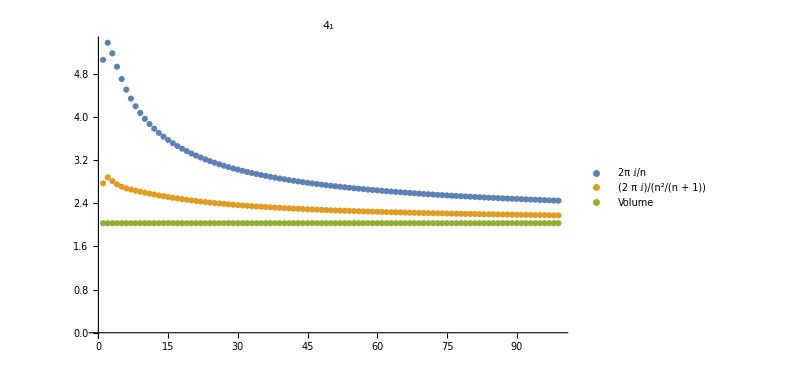

```mathematica
img41=ListPlot[{evals41,evals41guess,vol41plot},PlotRange->All,PlotLabel->"4_1",LabelStyle->Directive[FontSize->15,Black],PlotLegends->Placed[{"2π ⅈ/n","(2  π ⅈ)/(n^2/(n + 1))","Volume"},{.7,.7}],ImageSize->600]
```